```mathematica
k={0,-3,-4, -6,13, 17}
dim={1, x^2, y^2*x, y^4, y^2*x^3, x^4*y}
f1 = (Sin[7*(x+0.5)*(y+0.5)] + 1)/2  
f2 =LogisticSigmoid[Dot[k, dim]]
```

{0,-3,-4,-6,13,17}

{1,x^2,x y^2,y^4,x^3 y^2,x^4 y}

1/2 (1+Sin[7 (0.5+x) (0.5+y)])

LogisticSigmoid[-3 x^2+17 x^4 y-4 x y^2+13 x^3 y^2-6 y^4]

```mathematica
{1,x^2,x y^2,y^4,x^3 y^2,x^4 y}
```

{1,x^2,x y^2,y^4,x^3 y^2,x^4 y}

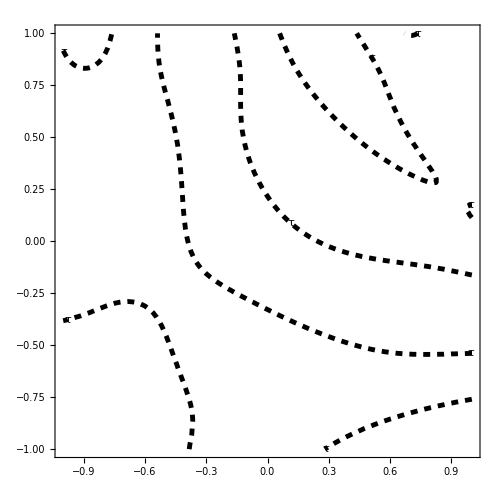

```mathematica
con = ContourPlot[ 
f1- f2,{x, -1, 1}, {y, -1, 1}, 
Contours-> {0.3},
ContourStyle->{
{Black,  Thickness[0.007]},
{Black, Dashed, Thickness[0.007]}},
ContourShading->None,
ContourLabels->(Text[Framed[Style["τ", FontSize->20],Background->Directive[Opacity[0.8], White],  FrameStyle-> None, ContentPadding->False, RoundingRadius->5], {#1, #2} ]&),
Prolog->Inset[Rasterize[DensityPlot[ 
f1 - f2,
{x, -1, 1}, {y, -1, 1},
ColorFunction->ColorData["SunsetColors"]
,PlotLegends->False,
FrameTicksStyle->Directive[FontSize-> 0, FontOpacity-> 0],
Frame->False
],
ImageSize->495
],
{0, 0}
],
ImageSize->500,
PlotRangePadding->0.05,
PlotLegends->Placed[BarLegend[{"SunsetColors", {-1, 1}}, LegendMarkerSize->{300, 30}, LabelStyle->Directive[FontSize -> 15, FontColor-> Black]], Bottom],
FrameTicksStyle->Directive[FontSize-> 0, FontOpacity-> 0]
]
```

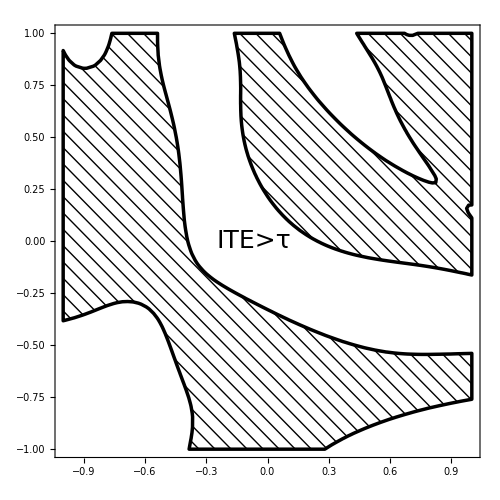

```mathematica
reg = RegionPlot[ 
f1- f2 < 0.3,{x, -1, 1}, {y, -1, 1}, 
BoundaryStyle->{
{Black,  Thickness[0.005]}},
MeshFunctions->{#1+#2&},
Mesh->{Range[-2 Pi,2 Pi,Pi/40]},MeshStyle->{Black},PlotStyle->None,
Epilog->Text[Style["ITE" > τ,25],{-0.25,0},Left,{1,0}],
Prolog->Inset[Rasterize[DensityPlot[ 
f1 - f2,
{x, -1, 1}, {y, -1, 1},
ColorFunction->ColorData["SunsetColors"]
,PlotLegends->False,
FrameTicksStyle->Directive[FontSize-> 0, FontOpacity-> 0],
Frame->False
],
ImageSize->495
],
{0, 0}
],
ImageSize->500,
PlotRangePadding->0.05,
PlotLegends->Placed[BarLegend[{"SunsetColors", {-1, 1}}, LegendMarkerSize->{300, 30}, LabelStyle->Directive[FontSize -> 15, FontColor-> Black]], Bottom],
FrameTicksStyle->Directive[FontSize-> 0, FontOpacity-> 0]

]
```

```mathematica
Export["heatmap02.pdf", reg]
```

heatmap02.pdf